```mathematica
Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"];
InstallFeynCalc[]
```

Welcome to the automatic FeynCalc installer brought to you by the FeynCalc developer team!

• To install the current stable version of FeynCalc (recommended for productive use), please evaluate

InstallFeynCalc[]

• To install the development version of FeynCalc (only for experts or beta testers), please evaluate

InstallFeynCalc[InstallFeynCalcDevelopmentVersion->True]

Downloading FeynCalc from https://github.com/FeynCalc/feyncalc/archive/hotfix-stable.zip ...done! 
FeynCalc zip file was saved to C:\Users\Farkas Borbála\AppData\Local\Temp\m-5bbce4b8-9adb-4f46-81fe-098defd33df1.
Extracting FeynCalc zip file to C:\Users\Farkas Borbála\AppData\Local\Temp\m-5bbce4b8-9adb-4f46-81fe-098defd33df1.dir ...Checking the directory structure...done! 
Copying FeynCalc to C:\Users\Farkas Borbála\AppData\Roaming\Mathematica\Applications\FeynCalc ...done! 
Setting up the format type of new output cells ... done! 
Creating the configuration file ... done! 
Downloading FeynArts from https://github.com/FeynCalc/feynarts-mirror/archive/master.zip ...done! 
FeynArts zip file was saved to C:\Users\Farkas Borbála\AppData\Local\Temp\m-37cda7ef-24c0-4aeb-b01f-a349f51d955f.
Extracting FeynArts zip file to C:\Users\Farkas Borbála\AppData\Roaming\Mathematica\Applications\FeynCalc\FeynArts ...done! 
Copying FeynArts to C:\Users\Farkas Borbála\AppData\Roaming\Mathematica\Applications\FeynCalc\FeynArts ...done! 

Installation complete! Loading FeynCalc ... 
Successfully patched FeynArts.

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

#### Definitions

Mandelstam variables :

```mathematica
mandelstam={Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 1]']]->(Subscript[m, ν]^2+Subscript[m, e]^2-t)/2,Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 2]]]->(s-Subscript[m, ν]^2-Subscript[m, n]^2)/2,Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 2]']]->(s+t-Subscript[m, n]^2-Subscript[m, e]^2)/2,Pair[Momentum[Subscript[p, 1]'],Momentum[Subscript[p, 2]]]->(s+t-Subscript[m, ν]^2-Subscript[m, Σ]^2)/2,Pair[Momentum[Subscript[p, 1]'],Momentum[Subscript[p, 2]']]->(s-Subscript[m, e]^2-Subscript[m, Σ]^2)/2,Pair[Momentum[Subscript[p, 2]],Momentum[Subscript[p, 2]']]->(Subscript[m, n]^2+Subscript[m, Σ]^2-t)/2, Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 1]]]->Subscript[m, ν]^2, Pair[Momentum[Subscript[p, 1]'],Momentum[Subscript[p, 1]']]->Subscript[m, e]^2,FeynAmpDenominator[StandardPropagatorDenominator[Momentum[Subscript[p, 1],D]-Momentum[Subscript[p, 1]',D],0,-Subscript[m, W]^2,{1,1}],StandardPropagatorDenominator[Momentum[Subscript[p, 1],D]-Momentum[Subscript[p, 1]',D],0,-Subscript[m, W]^2,{1,1}]]->1/((t-Subscript[m, W]^2)^2)}
```

{(p̄)_1·OverBar[p_1']→1/2 (m_e^2+m_ν^2-t),(p̄)_1·(p̄)_2→1/2 (-m_ν^2-m_n^2+s),(p̄)_1·OverBar[p_2']→1/2 (-m_e^2-m_n^2+s+t),(p̄)_2·OverBar[p_1']→1/2 (-m_ν^2-m_Σ^2+s+t),OverBar[p_1']·OverBar[p_2']→1/2 (-m_e^2-m_Σ^2+s),(p̄)_2·OverBar[p_2']→1/2 (m_n^2+m_Σ^2-t),((p̄)_1)^2→m_ν^2,OverBar[p_1']^2→m_e^2,1/(((p_1-p_1')^2-m_W^2+ⅈ η)^2)→1/((t-m_W^2)^2)}

Physical values :

```mathematica
setphysics={Subscript[m, W]->80.377,Subscript[m, e]->0.51100*10^{-3},Subscript[m, ν]->0,Subscript[m, Σ]->1197.4*10^{-3},Subscript[m, n]->939.57*10^{-3},Subscript[m, p]->938.27*10^{-3},Subscript[m, Λ]->1115.7*10^{-3},Subscript[V, us]->0.22430,d->0.80,f->0.46,g->0.652,Subscript[g, W]->0.652}
```

{m_W→80.377,m_e→{0.000511},m_ν→0,m_Σ→{1.1974},m_n→{0.93957},m_p→{0.93827},m_Λ→{1.1157},V_us→0.2243,d→0.8,f→0.46,g→0.652,g_W→0.652}

### Calculate the cross section (ν̄)_e n->e^+Σ^-

```mathematica
sa=g Conjugate[g] Subscript[g, W] Conjugate[Subscript[g, W]] Subscript[V, us] Conjugate[Subscript[V, us]] TR[(GS[Subscript[p, 1]]-Subscript[m, ν]).GA[ν].(1-GA[5]).(GS[Subscript[p, 1]']-Subscript[m, e]).GA[ν'] .(1-GA[5])]TR[(GS[Subscript[p, 2]']+Subscript[m, Σ]). ( GA[μ]+(d-f)GA[μ,5]).(GS[Subscript[p, 2]]+Subscript[m, n]).( GA[μ']+(d-f)GA[μ'].GA[5])](( -I SFAD[{Subscript[p, 1]-Subscript[p, 1]',Subscript[m, W]^2}])(MetricTensor[μ,ν]-(FV[Subscript[p, 1]-Subscript[p, 1]',μ]FV[Subscript[p, 1]-Subscript[p, 1]',ν])/Subscript[m, W]^2))(( -I SFAD[{Subscript[p, 1]-Subscript[p, 1]',Subscript[m, W]^2}])(MetricTensor[μ',ν']-(FV[Subscript[p, 1]-Subscript[p, 1]',μ']FV[Subscript[p, 1]-Subscript[p, 1]',ν'])/Subscript[m, W]^2))//Calc//Simplify
```

(32 g Conjugate[g] Conjugate[(g_W)] Conjugate[(V_us)] g_W (-2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+4 d ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+4 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-4 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-2 d^2 ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4-2 f^2 ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4+4 d f ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4+2 ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4+2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2+2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-4 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2-2 f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2+4 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2+2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2+d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-2 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-2 d^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2-2 f^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+4 d f ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2-2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 ((p̄)_1·(p̄)_2) ((2 (d^2-2 f d+f^2+1) ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2+(OverBar[p_1']·OverBar[p_2']) ((d-f+1)^2 m_W^2-(d^2-2 f d+f^2+1) OverBar[p_1']^2)) m_W^2+(d^2-2 f d+f^2+1) ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2']))+d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ+f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ-2 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ-((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ-2 d^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ-2 f^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ+4 d f ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ+2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ+((p̄)_1)^4 ((p̄)_1·OverBar[p_1']-2 OverBar[p_1']^2) ((d^2-2 f d+f^2+1) ((p̄)_2·OverBar[p_2'])+(d^2-2 f d+f^2-1) m_n m_Σ)-2 ((p̄)_1)^2 (((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d^2-((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d^2-2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d^2+2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d^2-2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d^2-2 OverBar[p_1']^2 m_n m_W^2 m_Σ d^2+OverBar[p_1']^4 m_n m_Σ d^2-2 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d+2 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d+4 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d-4 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d-4 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d+4 f ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d+4 f OverBar[p_1']^2 m_n m_W^2 m_Σ d-2 f OverBar[p_1']^4 m_n m_Σ d+f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-2 f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+2 f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2+2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2+2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-2 f^2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+(d^2-2 f d+f^2+1) ((p̄)_1·(p̄)_2) (-2 ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2+((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2'])+(OverBar[p_1']·OverBar[p_2']) (2 OverBar[p_1']^2-m_W^2))-2 f^2 OverBar[p_1']^2 m_n m_W^2 m_Σ+2 OverBar[p_1']^2 m_n m_W^2 m_Σ+f^2 OverBar[p_1']^4 m_n m_Σ-OverBar[p_1']^4 m_n m_Σ+((p̄)_1·OverBar[p_1'])^2 ((d^2-2 f d+f^2+1) ((p̄)_2·OverBar[p_2'])+(d^2-2 f d+f^2-1) m_n m_Σ)+((p̄)_1·OverBar[p_1']) (((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d^2+m_n m_W^2 m_Σ d^2-3 OverBar[p_1']^2 m_n m_Σ d^2-2 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d-2 f m_n m_W^2 m_Σ d+6 f OverBar[p_1']^2 m_n m_Σ d-(d^2-2 f d+f^2+1) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1'])+f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])+((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])-(d^2-2 f d+f^2+1) ((p̄)_2·OverBar[p_2']) (3 OverBar[p_1']^2-m_W^2)+f^2 m_n m_W^2 m_Σ-m_n m_W^2 m_Σ-3 f^2 OverBar[p_1']^2 m_n m_Σ+3 OverBar[p_1']^2 m_n m_Σ))) V_us)/(((p_1-p_1')^2-m_W^2+ⅈ η)^2 m_W^4)

Then, calculate the cross section dσ/dt=1/(64πs)1/(|p_(1_CM)|^2)(|𝒯|)^2

```mathematica
cs=1/(64π s) s/(Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 2]]]^2-Subscript[m, ν]^2 Subscript[m, n]^2)sa
```

(g Conjugate[g] Conjugate[(g_W)] Conjugate[(V_us)] g_W (-2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+4 d ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+4 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-4 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-2 d^2 ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4-2 f^2 ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4+4 d f ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4+2 ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4+2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2+2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-4 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2-2 f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2+4 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2+2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2+d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-2 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-2 d^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2-2 f^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+4 d f ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2-2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 ((p̄)_1·(p̄)_2) ((2 (d^2-2 f d+f^2+1) ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2+(OverBar[p_1']·OverBar[p_2']) ((d-f+1)^2 m_W^2-(d^2-2 f d+f^2+1) OverBar[p_1']^2)) m_W^2+(d^2-2 f d+f^2+1) ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2']))+d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ+f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ-2 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ-((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ-2 d^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ-2 f^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ+4 d f ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ+2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ+((p̄)_1)^4 ((p̄)_1·OverBar[p_1']-2 OverBar[p_1']^2) ((d^2-2 f d+f^2+1) ((p̄)_2·OverBar[p_2'])+(d^2-2 f d+f^2-1) m_n m_Σ)-2 ((p̄)_1)^2 (((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d^2-((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d^2-2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d^2+2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d^2-2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d^2-2 OverBar[p_1']^2 m_n m_W^2 m_Σ d^2+OverBar[p_1']^4 m_n m_Σ d^2-2 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d+2 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d+4 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d-4 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d-4 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d+4 f ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d+4 f OverBar[p_1']^2 m_n m_W^2 m_Σ d-2 f OverBar[p_1']^4 m_n m_Σ d+f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-2 f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+2 f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2+2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2+2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-2 f^2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+(d^2-2 f d+f^2+1) ((p̄)_1·(p̄)_2) (-2 ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2+((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2'])+(OverBar[p_1']·OverBar[p_2']) (2 OverBar[p_1']^2-m_W^2))-2 f^2 OverBar[p_1']^2 m_n m_W^2 m_Σ+2 OverBar[p_1']^2 m_n m_W^2 m_Σ+f^2 OverBar[p_1']^4 m_n m_Σ-OverBar[p_1']^4 m_n m_Σ+((p̄)_1·OverBar[p_1'])^2 ((d^2-2 f d+f^2+1) ((p̄)_2·OverBar[p_2'])+(d^2-2 f d+f^2-1) m_n m_Σ)+((p̄)_1·OverBar[p_1']) (((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d^2+m_n m_W^2 m_Σ d^2-3 OverBar[p_1']^2 m_n m_Σ d^2-2 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d-2 f m_n m_W^2 m_Σ d+6 f OverBar[p_1']^2 m_n m_Σ d-(d^2-2 f d+f^2+1) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1'])+f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])+((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])-(d^2-2 f d+f^2+1) ((p̄)_2·OverBar[p_2']) (3 OverBar[p_1']^2-m_W^2)+f^2 m_n m_W^2 m_Σ-m_n m_W^2 m_Σ-3 f^2 OverBar[p_1']^2 m_n m_Σ+3 OverBar[p_1']^2 m_n m_Σ))) V_us)/(2 π ((p_1-p_1')^2-m_W^2+ⅈ η)^2 m_W^4 (((p̄)_1·(p̄)_2)^2-m_n^2 m_ν^2))

Substitute the Mandelstam variables.

```mathematica
csmandelstam=cs/.mandelstam//Simplify
```

-((g Conjugate[g] Conjugate[(g_W)] Conjugate[(V_us)] g_W (((d^2-2 f d+f^2+1) m_n^4-(d^2-2 f d+f^2+1) (-4 m_W^2+2 m_Σ^2+t) m_n^2-2 (d^2-2 f d+f^2-1) (t-2 m_W^2) m_Σ m_n+(d^2-2 f d+f^2+1) m_Σ^2 (m_Σ^2-t)) m_e^4+(-((d^2-2 f d+f^2+1) (-4 m_W^2+2 m_ν^2+t) m_n^4)+(2 (d-f+1)^2 m_W^4-4 (d^2-2 f d+f^2+1) (m_ν^2+m_Σ^2+s+t) m_W^2+(d^2-2 f d+f^2+1) (2 m_ν^2+t) (2 m_Σ^2+t)) m_n^2+2 (d^2-2 f d+f^2-1) (2 m_W^4-2 (2 m_ν^2+t) m_W^2+t (2 m_ν^2+t)) m_Σ m_n-4 d^2 s m_W^4-4 f^2 s m_W^4+8 d f s m_W^4-4 s m_W^4-2 d^2 t m_W^4-2 f^2 t m_W^4+4 d t m_W^4+4 d f t m_W^4-4 f t m_W^4-2 t m_W^4-2 d^2 m_ν^2 m_Σ^4-2 f^2 m_ν^2 m_Σ^4+4 d f m_ν^2 m_Σ^4-2 m_ν^2 m_Σ^4-d^2 t m_Σ^4-f^2 t m_Σ^4+2 d f t m_Σ^4-t m_Σ^4+4 d^2 m_W^4 m_ν^2+4 f^2 m_W^4 m_ν^2-8 d f m_W^4 m_ν^2+4 m_W^4 m_ν^2+2 d^2 m_W^4 m_Σ^2+2 f^2 m_W^4 m_Σ^2-4 d m_W^4 m_Σ^2-4 d f m_W^4 m_Σ^2+4 f m_W^4 m_Σ^2+2 m_W^4 m_Σ^2+d^2 t^2 m_Σ^2+f^2 t^2 m_Σ^2-2 d f t^2 m_Σ^2+t^2 m_Σ^2+4 d^2 s m_W^2 m_Σ^2+4 f^2 s m_W^2 m_Σ^2-8 d f s m_W^2 m_Σ^2+4 s m_W^2 m_Σ^2-4 d^2 m_W^2 m_ν^2 m_Σ^2-4 f^2 m_W^2 m_ν^2 m_Σ^2+8 d f m_W^2 m_ν^2 m_Σ^2-4 m_W^2 m_ν^2 m_Σ^2+2 d^2 t m_ν^2 m_Σ^2+2 f^2 t m_ν^2 m_Σ^2-4 d f t m_ν^2 m_Σ^2+2 t m_ν^2 m_Σ^2) m_e^2+4 m_W^2 m_ν^2 ((d^2-2 f d+f^2+1) (s-m_Σ^2) m_n^2-(d^2-2 f d+f^2-1) (t-m_ν^2) m_Σ m_n+(d^2-2 f d+f^2+1) m_Σ^2 (m_ν^2+m_Σ^2-s-t))+m_ν^2 (t-m_ν^2) (-((d^2-2 f d+f^2+1) m_n^4)+(d^2-2 f d+f^2+1) (2 m_Σ^2+t) m_n^2+2 (d^2-2 f d+f^2-1) t m_Σ m_n+(d^2-2 f d+f^2+1) m_Σ^2 (t-m_Σ^2))+2 m_W^4 (2 s^2 d^2+t^2 d^2-2 s m_Σ^2 d^2-t m_Σ^2 d^2+2 s t d^2-4 f s^2 d-2 f t^2 d-2 t^2 d+4 f s m_Σ^2 d+2 f t m_Σ^2 d+2 t m_Σ^2 d-4 f s t d-4 s t d+2 f^2 s^2+2 s^2+f^2 t^2+2 f t^2+t^2-2 f^2 s m_Σ^2-2 s m_Σ^2-f^2 t m_Σ^2-2 f t m_Σ^2-t m_Σ^2+2 f^2 s t+4 f s t+2 s t-2 (d^2-2 f d+f^2-1) m_n (t-m_ν^2) m_Σ-m_ν^2 (t (-d+f+1)^2-(d-f+1)^2 m_Σ^2+2 (d^2-2 f d+f^2+1) s)+m_n^2 (-2 s d^2-t d^2+4 f s d+2 f t d+2 t d+(-d+f+1)^2 m_ν^2+2 (d^2-2 f d+f^2+1) m_Σ^2-2 f^2 s-2 s-f^2 t-2 f t-t))) V_us)/(2 π m_W^4 (t-m_W^2)^2 (m_n^4-2 (m_ν^2+s) m_n^2+(s-m_ν^2)^2)))

Define the limits of integration.

```mathematica
t0=((Subscript[m, ν]^2-Subscript[m, e]^2-Subscript[m, n]^2+Subscript[m, Σ]^2)/(2Sqrt[s]))^2-(Sqrt[((s+Subscript[m, ν]^2-Subscript[m, n]^2)/(2Sqrt[s]))^2-Subscript[m, ν]^2]-Sqrt[((s+Subscript[m, e]^2-Subscript[m, Σ]^2)/(2Sqrt[s]))^2-Subscript[m, e]^2])^2/.setphysics;
t1=((Subscript[m, ν]^2-Subscript[m, e]^2-Subscript[m, n]^2+Subscript[m, Σ]^2)/(2Sqrt[s]))^2-(Sqrt[((s+Subscript[m, ν]^2-Subscript[m, n]^2)/(2Sqrt[s]))^2-Subscript[m, ν]^2]+Sqrt[((s+Subscript[m, e]^2-Subscript[m, Σ]^2)/(2Sqrt[s]))^2-Subscript[m, e]^2])^2/.setphysics;
t0f[s_]:=Evaluate[t0[[1]]]

t1f[s_]:=Evaluate[t1[[1]]]
```

Substitute values of constants and masses in GeV.

```mathematica
csmandelstamsubstitued=csmandelstam/.setphysics
crf[s_]:=Evaluate[csmandelstamsubstitued[[1]]]
```

{-((3.4669×10^-11 (6.81842×10^-14 (1.59951 (1.43377-t)-0.984843 (t-25839.)+1.98997 (t-12920.9)+0.869411)+8.34751×10^7 (2.2312 s^2+0.8712 s t+0.882792 (-2.2312 s-0.4356 t+3.19902)-3.19902 s+0.4356 t^2+1.36542 t)+2.61121×10^-7 (0.882792 (-28829.2 (s+t+1.43377)+1.1156 t (t+2.86753)+1.49888×10^8)-1.86208×10^8 s+1.59951 t^2-1.98997 (t^2-12920.9 t+8.34751×10^7)-3.63618×10^7 t-0.869411 (t-25841.8)+5.21343×10^7)+0.))/((s^2-1.76558 s+0.779321) (t-6460.46)^2))}

Define the integration and limits.
The minimum and maximum energy:
lower limit: ((m_e+m_Σ))^2
upper limit: m_n(m_n+2)

```mathematica
sigma[s_?NumericQ]:=NIntegrate[crf[s],{t,t0f[s],t1f[s]}]
lower=(Subscript[m, e]+Subscript[m, Σ])^2/.setphysics;(*(0.51100*10^{-3}+1197.4*10^{-3})^2;*)
upper=Subscript[m, n](Subscript[m, n]+2)/.setphysics;(*939.57*10^{-3}(939.57*10^{-3}+2);*)
lower[[1]]
upper[[1]]
```

1.43499

2.76193

Plot the cross section in terms of energy.

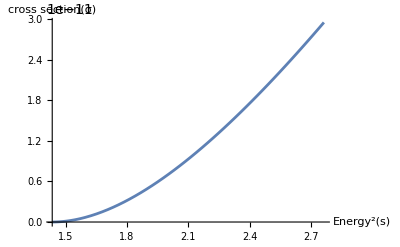

```mathematica
Plot[0.4*sigma[s],{s,lower[[1]],upper[[1]]}, Axes->True,AxesLabel->{(Energy^2)[s],cross section[σ]}]
```

### Calculate the cross section (ν̄)_e p->e^+Λ

```mathematica
sa=g Conjugate[g] Subscript[g, W] Conjugate[Subscript[g, W]] Subscript[V, us] Conjugate[Subscript[V, us]] TR[(GS[Subscript[p, 1]]-Subscript[m, ν]).GA[ν].(1-GA[5]).(GS[Subscript[p, 1]']-Subscript[m, e]).GA[ν'] .(1-GA[5])]TR[(GS[Subscript[p, 2]']+Subscript[m, Λ]). ( Sqrt[6]/2 GA[μ]+(-1/Sqrt[6]d-3/Sqrt[6] f)GA[μ,5]).(GS[Subscript[p, 2]]+Subscript[m, p]).(Sqrt[6]/2 GA[μ']+(-1/Sqrt[6]d-3/Sqrt[6] f)GA[μ'].GA[5])](( -I SFAD[{Subscript[p, 1]-Subscript[p, 1]',Subscript[m, W]^2}])(MetricTensor[μ,ν]-(FV[Subscript[p, 1]-Subscript[p, 1]',μ]FV[Subscript[p, 1]-Subscript[p, 1]',ν])/Subscript[m, W]^2))(( -I SFAD[{Subscript[p, 1]-Subscript[p, 1]',Subscript[m, W]^2}])(MetricTensor[μ',ν']-(FV[Subscript[p, 1]-Subscript[p, 1]',μ']FV[Subscript[p, 1]-Subscript[p, 1]',ν'])/Subscript[m, W]^2))//Calc//Simplify
```

-((16 g Conjugate[g] Conjugate[(g_W)] Conjugate[(V_us)] g_W (2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+18 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+12 d ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+12 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+36 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+18 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+2 d^2 ((p̄)_1·OverBar[p_1']) m_p m_Λ m_W^4+18 f^2 ((p̄)_1·OverBar[p_1']) m_p m_Λ m_W^4+12 d f ((p̄)_1·OverBar[p_1']) m_p m_Λ m_W^4-18 ((p̄)_1·OverBar[p_1']) m_p m_Λ m_W^4-2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-18 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-12 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-18 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2+2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+18 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+12 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+18 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+2 d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_p m_Λ m_W^2+18 f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_p m_Λ m_W^2+12 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_p m_Λ m_W^2-18 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_p m_Λ m_W^2-d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-9 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-6 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-9 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-18 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-12 d f ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-18 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 d^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+18 f^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+12 d f ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+18 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+18 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+12 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+18 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+2 ((p̄)_1·(p̄)_2) ((2 (d^2+6 f d+9 f^2+9) ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2-(OverBar[p_1']·OverBar[p_2']) ((d^2+6 f d+9 f^2+9) OverBar[p_1']^2-(d+3 f-3)^2 m_W^2)) m_W^2+(d^2+6 f d+9 f^2+9) ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2']))-d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_p m_Λ-9 f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_p m_Λ-6 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_p m_Λ+9 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_p m_Λ+2 d^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_p m_Λ+18 f^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_p m_Λ+12 d f ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_p m_Λ-18 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_p m_Λ-((p̄)_1)^4 ((p̄)_1·OverBar[p_1']-2 OverBar[p_1']^2) ((d^2+6 f d+9 f^2+9) ((p̄)_2·OverBar[p_2'])+(d^2+6 f d+9 f^2-9) m_p m_Λ)+2 ((p̄)_1)^2 (((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d^2-((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d^2-2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d^2+2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d^2-2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d^2-2 OverBar[p_1']^2 m_p m_W^2 m_Λ d^2+OverBar[p_1']^4 m_p m_Λ d^2+6 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d-6 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d-12 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d+12 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d+12 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d-12 f ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d-12 f OverBar[p_1']^2 m_p m_W^2 m_Λ d+6 f OverBar[p_1']^4 m_p m_Λ d+9 f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+9 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-9 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-9 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-18 f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-18 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+18 f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2+18 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2+18 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+18 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-18 f^2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-18 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+(d^2+6 f d+9 f^2+9) ((p̄)_1·(p̄)_2) (-2 ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2+((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2'])+(OverBar[p_1']·OverBar[p_2']) (2 OverBar[p_1']^2-m_W^2))-18 f^2 OverBar[p_1']^2 m_p m_W^2 m_Λ+18 OverBar[p_1']^2 m_p m_W^2 m_Λ+9 f^2 OverBar[p_1']^4 m_p m_Λ-9 OverBar[p_1']^4 m_p m_Λ+((p̄)_1·OverBar[p_1'])^2 ((d^2+6 f d+9 f^2+9) ((p̄)_2·OverBar[p_2'])+(d^2+6 f d+9 f^2-9) m_p m_Λ)+((p̄)_1·OverBar[p_1']) (((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d^2+m_p m_W^2 m_Λ d^2-3 OverBar[p_1']^2 m_p m_Λ d^2+6 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d+6 f m_p m_W^2 m_Λ d-18 f OverBar[p_1']^2 m_p m_Λ d-(d^2+6 f d+9 f^2+9) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1'])+9 f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])+9 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])-(d^2+6 f d+9 f^2+9) ((p̄)_2·OverBar[p_2']) (3 OverBar[p_1']^2-m_W^2)+9 f^2 m_p m_W^2 m_Λ-9 m_p m_W^2 m_Λ-27 f^2 OverBar[p_1']^2 m_p m_Λ+27 OverBar[p_1']^2 m_p m_Λ))) V_us)/(3 ((p_1-p_1')^2-m_W^2+ⅈ η)^2 m_W^4))

Then, calculate the cross section dσ/dt=1/(64πs)1/(|p_(1_CM)|^2)(|𝒯|)^2

```mathematica
cs=1/(64π s) s/(Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 2]]]^2-Subscript[m, ν]^2 Subscript[m, p]^2)sa
```

-((g Conjugate[g] Conjugate[(g_W)] Conjugate[(V_us)] g_W (2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+18 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+12 d ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+12 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+36 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+18 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+2 d^2 ((p̄)_1·OverBar[p_1']) m_p m_Λ m_W^4+18 f^2 ((p̄)_1·OverBar[p_1']) m_p m_Λ m_W^4+12 d f ((p̄)_1·OverBar[p_1']) m_p m_Λ m_W^4-18 ((p̄)_1·OverBar[p_1']) m_p m_Λ m_W^4-2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-18 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-12 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-18 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2+2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+18 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+12 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+18 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+2 d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_p m_Λ m_W^2+18 f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_p m_Λ m_W^2+12 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_p m_Λ m_W^2-18 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_p m_Λ m_W^2-d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-9 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-6 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-9 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-18 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-12 d f ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-18 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 d^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+18 f^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+12 d f ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+18 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+18 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+12 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+18 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+2 ((p̄)_1·(p̄)_2) ((2 (d^2+6 f d+9 f^2+9) ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2-(OverBar[p_1']·OverBar[p_2']) ((d^2+6 f d+9 f^2+9) OverBar[p_1']^2-(d+3 f-3)^2 m_W^2)) m_W^2+(d^2+6 f d+9 f^2+9) ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2']))-d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_p m_Λ-9 f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_p m_Λ-6 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_p m_Λ+9 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_p m_Λ+2 d^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_p m_Λ+18 f^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_p m_Λ+12 d f ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_p m_Λ-18 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_p m_Λ-((p̄)_1)^4 ((p̄)_1·OverBar[p_1']-2 OverBar[p_1']^2) ((d^2+6 f d+9 f^2+9) ((p̄)_2·OverBar[p_2'])+(d^2+6 f d+9 f^2-9) m_p m_Λ)+2 ((p̄)_1)^2 (((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d^2-((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d^2-2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d^2+2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d^2-2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d^2-2 OverBar[p_1']^2 m_p m_W^2 m_Λ d^2+OverBar[p_1']^4 m_p m_Λ d^2+6 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d-6 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d-12 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d+12 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d+12 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d-12 f ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d-12 f OverBar[p_1']^2 m_p m_W^2 m_Λ d+6 f OverBar[p_1']^4 m_p m_Λ d+9 f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+9 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-9 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-9 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-18 f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-18 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+18 f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2+18 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2+18 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+18 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-18 f^2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-18 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+(d^2+6 f d+9 f^2+9) ((p̄)_1·(p̄)_2) (-2 ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2+((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2'])+(OverBar[p_1']·OverBar[p_2']) (2 OverBar[p_1']^2-m_W^2))-18 f^2 OverBar[p_1']^2 m_p m_W^2 m_Λ+18 OverBar[p_1']^2 m_p m_W^2 m_Λ+9 f^2 OverBar[p_1']^4 m_p m_Λ-9 OverBar[p_1']^4 m_p m_Λ+((p̄)_1·OverBar[p_1'])^2 ((d^2+6 f d+9 f^2+9) ((p̄)_2·OverBar[p_2'])+(d^2+6 f d+9 f^2-9) m_p m_Λ)+((p̄)_1·OverBar[p_1']) (((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d^2+m_p m_W^2 m_Λ d^2-3 OverBar[p_1']^2 m_p m_Λ d^2+6 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d+6 f m_p m_W^2 m_Λ d-18 f OverBar[p_1']^2 m_p m_Λ d-(d^2+6 f d+9 f^2+9) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1'])+9 f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])+9 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])-(d^2+6 f d+9 f^2+9) ((p̄)_2·OverBar[p_2']) (3 OverBar[p_1']^2-m_W^2)+9 f^2 m_p m_W^2 m_Λ-9 m_p m_W^2 m_Λ-27 f^2 OverBar[p_1']^2 m_p m_Λ+27 OverBar[p_1']^2 m_p m_Λ))) V_us)/(12 π ((p_1-p_1')^2-m_W^2+ⅈ η)^2 m_W^4 (((p̄)_1·(p̄)_2)^2-m_p^2 m_ν^2)))

Substitute the Mandelstam variables.

```mathematica
csmandelstam=cs/.mandelstam/.{Subscript[m, n]->Subscript[m, p],Subscript[m, Σ]->Subscript[m, Λ]}//Simplify
```

-((g Conjugate[g] Conjugate[(g_W)] Conjugate[(V_us)] g_W (((d^2+2 f d+f^2+1) m_p^4+(8 (d+f)^2 m_W^2-2 (d^2+2 f d+f^2+1) m_Λ^2-(3 d^2+6 f d+3 f^2-1) t) m_p^2+(d^2+2 f d+f^2+1) m_Λ^2 (m_Λ^2-t)) m_e^4+(-((d^2+2 f d+f^2+1) (-4 m_W^2+2 m_ν^2+t) m_p^4)+(2 (3 d^2+(6 f-2) d+3 f^2-2 f-1) m_W^4-4 (s d^2+2 t d^2+2 f s d+4 f t d+(d^2+2 f d+f^2+1) m_Λ^2+(3 d^2+6 f d+3 f^2-1) m_ν^2+f^2 s+s+2 f^2 t) m_W^2+(2 (d^2+2 f d+f^2+1) m_Λ^2+(3 d^2+6 f d+3 f^2-1) t) (2 m_ν^2+t)) m_p^2+4 (d^2+2 f d+f^2+1) m_W^2 m_Λ^2 (s-m_ν^2)+(d^2+2 f d+f^2+1) m_Λ^2 (t-m_Λ^2) (2 m_ν^2+t)-2 m_W^4 (2 s d^2+t d^2+4 f s d+2 f t d+2 t d-(d+f+1)^2 m_Λ^2-2 (d^2+2 f d+f^2+1) m_ν^2+2 f^2 s+2 s+f^2 t+2 f t+t)) m_e^2+(-((d^2+2 f d+f^2+1) m_p^4)+(2 (d^2+2 f d+f^2+1) m_Λ^2+(3 d^2+6 f d+3 f^2-1) t) m_p^2+(d^2+2 f d+f^2+1) m_Λ^2 (t-m_Λ^2)) m_ν^2 (t-m_ν^2)+4 m_W^2 m_ν^2 ((s d^2-t d^2+2 f s d-2 f t d-(d^2+2 f d+f^2+1) m_Λ^2+(d^2+2 f d+f^2-1) m_ν^2+f^2 s+s-f^2 t+t) m_p^2+(d^2+2 f d+f^2+1) m_Λ^2 (m_Λ^2+m_ν^2-s-t))+2 m_W^4 (2 s^2 d^2+t^2 d^2-2 s m_ν^2 d^2-t m_ν^2 d^2+2 s t d^2+4 f s^2 d+2 f t^2 d+2 t^2 d-4 f s m_ν^2 d-2 f t m_ν^2 d-2 t m_ν^2 d+4 f s t d+4 s t d+2 f^2 s^2+2 s^2+f^2 t^2+2 f t^2+t^2-2 f^2 s m_ν^2-2 s m_ν^2-f^2 t m_ν^2-2 f t m_ν^2-t m_ν^2+2 f^2 s t+4 f s t+2 s t-m_Λ^2 (t (d+f+1)^2-(d+f-1)^2 m_ν^2+2 (d^2+2 f d+f^2+1) s)+m_p^2 (-2 s d^2-3 t d^2-4 f s d-6 f t d-2 t d+2 (d^2+2 f d+f^2+1) m_Λ^2+(3 d^2+6 f d+2 d+3 f^2+2 f-1) m_ν^2-2 f^2 s-2 s-3 f^2 t-2 f t+t))) V_us)/(2 π m_W^4 (t-m_W^2)^2 (m_p^4-2 (m_ν^2+s) m_p^2+(s-m_ν^2)^2)))

Define the limits of integration.

```mathematica
t0=((Subscript[m, ν]^2-Subscript[m, e]^2-Subscript[m, n]^2+Subscript[m, Σ]^2)/(2Sqrt[s]))^2-(Sqrt[((s+Subscript[m, ν]^2-Subscript[m, n]^2)/(2Sqrt[s]))^2-Subscript[m, ν]^2]-Sqrt[((s+Subscript[m, e]^2-Subscript[m, Σ]^2)/(2Sqrt[s]))^2-Subscript[m, e]^2])^2/.{Subscript[m, n]->Subscript[m, p],Subscript[m, Σ]->Subscript[m, Λ]}/.setphysics;
t1=((Subscript[m, ν]^2-Subscript[m, e]^2-Subscript[m, n]^2+Subscript[m, Σ]^2)/(2Sqrt[s]))^2-(Sqrt[((s+Subscript[m, ν]^2-Subscript[m, n]^2)/(2Sqrt[s]))^2-Subscript[m, ν]^2]+Sqrt[((s+Subscript[m, e]^2-Subscript[m, Σ]^2)/(2Sqrt[s]))^2-Subscript[m, e]^2])^2/.{Subscript[m, n]->Subscript[m, p],Subscript[m, Σ]->Subscript[m, Λ]}/.setphysics;
t0f[s_]:=Evaluate[t0[[1]]]

t1f[s_]:=Evaluate[t1[[1]]]
```

Substitute values of constants and masses in GeV.

```mathematica
csmandelstamsubstitued=csmandelstam/.setphysics
crf[s_]:=Evaluate[csmandelstamsubstitued[[1]]]
```

{-((3.4669×10^-11 (6.81842×10^-14 (0.880351 (82046.6-3.7628 t)+3.22101 (1.24479-t)+2.00543)+8.34751×10^7 (5.1752 s^2+10.2152 s t+0.880351 (-5.1752 s-6.2828 t+6.44202)-1.24479 (5.1752 s+5.1076 t+0.)+5.1076 t^2+0.)+2.61121×10^-7 (-8.34751×10^7 (5.1752 s+5.1076 t-6.35787)+0.880351 (-25841.8 (2.5876 s+3.1752 t+3.22101)+t (3.7628 t+6.44202)+1.03743×10^8)+83236.8 s-2.00543 (t-25841.8)+3.22101 (t-1.24479) t)+0.))/((s^2-1.7607 s+0.775017) (t-6460.46)^2))}

Define the integration and limits.
The minimum and maximum energy:
lower limit: ((m_e+m_Λ))^2
upper limit: m_p(m_p+2)

```mathematica
sigma[s_?NumericQ]:=NIntegrate[crf[s],{t,t0f[s],t1f[s]}]
lower=(Subscript[m, e]+Subscript[m, Σ])^2/.{Subscript[m, n]->Subscript[m, p],Subscript[m, Σ]->Subscript[m, Λ]}/.setphysics;(*(0.51100*10^{-3}+1197.4*10^{-3})^2;*)
upper=Subscript[m, n](Subscript[m, n]+2)/.{Subscript[m, n]->Subscript[m, p],Subscript[m, Σ]->Subscript[m, Λ]}/.setphysics;(*939.57*10^{-3}(939.57*10^{-3}+2);*)
lower[[1]]
upper[[1]]
```

1.24593

2.75689

Plot the cross section in terms of energy.

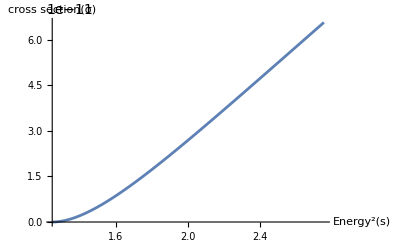

```mathematica
Plot[0.4*sigma[s],{s,lower[[1]],upper[[1]]}, Axes->True,AxesLabel->{(Energy^2)[s],cross section[σ]}]
```

### Calculate the cross section (ν̄)_e p->e^+n

```mathematica
sa=g Conjugate[g] Subscript[g, W] Conjugate[Subscript[g, W]] Subscript[V, us] Conjugate[Subscript[V, us]] TR[(GS[Subscript[p, 1]]-Subscript[m, ν]).GA[ν].(1-GA[5]).(GS[Subscript[p, 1]']-Subscript[m, e]).GA[ν'] .(1-GA[5])]TR[(GS[Subscript[p, 2]']+Subscript[m, n]). ( -GA[μ]+(d+f)GA[μ,5]).(GS[Subscript[p, 2]]+Subscript[m, p]).(- GA[μ']+(d+f)GA[μ'].GA[5])](( -I SFAD[{Subscript[p, 1]-Subscript[p, 1]',Subscript[m, W]^2}])(MetricTensor[μ,ν]-(FV[Subscript[p, 1]-Subscript[p, 1]',μ]FV[Subscript[p, 1]-Subscript[p, 1]',ν])/Subscript[m, W]^2))(( -I SFAD[{Subscript[p, 1]-Subscript[p, 1]',Subscript[m, W]^2}])(MetricTensor[μ',ν']-(FV[Subscript[p, 1]-Subscript[p, 1]',μ']FV[Subscript[p, 1]-Subscript[p, 1]',ν'])/Subscript[m, W]^2))//Calc//Simplify
```

-((32 g Conjugate[g] Conjugate[(g_W)] Conjugate[(V_us)] g_W (2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+4 d ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+4 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+4 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+2 d^2 ((p̄)_1·OverBar[p_1']) m_n m_p m_W^4+2 f^2 ((p̄)_1·OverBar[p_1']) m_n m_p m_W^4+4 d f ((p̄)_1·OverBar[p_1']) m_n m_p m_W^4-2 ((p̄)_1·OverBar[p_1']) m_n m_p m_W^4-2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-4 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2+2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+2 d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_p m_W^2+2 f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_p m_W^2+4 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_p m_W^2-2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_p m_W^2-d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-2 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 d^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+2 f^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+4 d f ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_p-f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_p-2 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_p+((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_p+2 d^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_p+2 f^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_p+4 d f ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_p-2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_p-((p̄)_1)^4 ((p̄)_1·OverBar[p_1']-2 OverBar[p_1']^2) ((d^2+2 f d+f^2+1) ((p̄)_2·OverBar[p_2'])+(d^2+2 f d+f^2-1) m_n m_p)+2 ((p̄)_1)^2 (((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d^2-((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d^2-2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d^2+2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d^2-2 OverBar[p_1']^2 m_n m_p m_W^2 d^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d^2-2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d^2+OverBar[p_1']^4 m_n m_p d^2+2 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d-2 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d-4 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d+4 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d-4 f OverBar[p_1']^2 m_n m_p m_W^2 d+4 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d-4 f ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d+2 f OverBar[p_1']^4 m_n m_p d+f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-2 f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+2 f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2+2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2-2 f^2 OverBar[p_1']^2 m_n m_p m_W^2+2 OverBar[p_1']^2 m_n m_p m_W^2+2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-2 f^2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+f^2 OverBar[p_1']^4 m_n m_p-OverBar[p_1']^4 m_n m_p+((p̄)_1·OverBar[p_1'])^2 ((d^2+2 f d+f^2+1) ((p̄)_2·OverBar[p_2'])+(d^2+2 f d+f^2-1) m_n m_p)+(d^2+2 f d+f^2+1) ((p̄)_1·(p̄)_2) (-2 ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2+((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2'])+(OverBar[p_1']·OverBar[p_2']) (2 OverBar[p_1']^2-m_W^2))+((p̄)_1·OverBar[p_1']) (m_n m_p m_W^2 d^2+((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d^2-3 OverBar[p_1']^2 m_n m_p d^2+2 f m_n m_p m_W^2 d+2 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d-6 f OverBar[p_1']^2 m_n m_p d+f^2 m_n m_p m_W^2-m_n m_p m_W^2-(d^2+2 f d+f^2+1) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1'])+f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])+((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])-3 f^2 OverBar[p_1']^2 m_n m_p+3 OverBar[p_1']^2 m_n m_p-(d^2+2 f d+f^2+1) ((p̄)_2·OverBar[p_2']) (3 OverBar[p_1']^2-m_W^2)))+2 ((p̄)_1·(p̄)_2) ((2 (d^2+2 f d+f^2+1) ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2-(OverBar[p_1']·OverBar[p_2']) ((d^2+2 f d+f^2+1) OverBar[p_1']^2-(d+f-1)^2 m_W^2)) m_W^2+(d^2+2 f d+f^2+1) ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2']))) V_us)/(((p_1-p_1')^2-m_W^2+ⅈ η)^2 m_W^4))

Then, calculate the cross section dσ/dt=1/(64πs)1/(|p_(1_CM)|^2)(|𝒯|)^2

```mathematica
cs=1/(64π s) s/(Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 2]]]^2-Subscript[m, ν]^2 Subscript[m, p]^2)sa
```

-((g Conjugate[g] Conjugate[(g_W)] Conjugate[(V_us)] g_W (2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+4 d ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+4 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+4 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+2 d^2 ((p̄)_1·OverBar[p_1']) m_n m_p m_W^4+2 f^2 ((p̄)_1·OverBar[p_1']) m_n m_p m_W^4+4 d f ((p̄)_1·OverBar[p_1']) m_n m_p m_W^4-2 ((p̄)_1·OverBar[p_1']) m_n m_p m_W^4-2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-4 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2+2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+2 d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_p m_W^2+2 f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_p m_W^2+4 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_p m_W^2-2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_p m_W^2-d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-2 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 d^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+2 f^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+4 d f ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_p-f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_p-2 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_p+((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_p+2 d^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_p+2 f^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_p+4 d f ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_p-2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_p-((p̄)_1)^4 ((p̄)_1·OverBar[p_1']-2 OverBar[p_1']^2) ((d^2+2 f d+f^2+1) ((p̄)_2·OverBar[p_2'])+(d^2+2 f d+f^2-1) m_n m_p)+2 ((p̄)_1)^2 (((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d^2-((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d^2-2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d^2+2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d^2-2 OverBar[p_1']^2 m_n m_p m_W^2 d^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d^2-2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d^2+OverBar[p_1']^4 m_n m_p d^2+2 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d-2 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d-4 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d+4 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d-4 f OverBar[p_1']^2 m_n m_p m_W^2 d+4 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d-4 f ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d+2 f OverBar[p_1']^4 m_n m_p d+f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-2 f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+2 f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2+2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2-2 f^2 OverBar[p_1']^2 m_n m_p m_W^2+2 OverBar[p_1']^2 m_n m_p m_W^2+2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-2 f^2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+f^2 OverBar[p_1']^4 m_n m_p-OverBar[p_1']^4 m_n m_p+((p̄)_1·OverBar[p_1'])^2 ((d^2+2 f d+f^2+1) ((p̄)_2·OverBar[p_2'])+(d^2+2 f d+f^2-1) m_n m_p)+(d^2+2 f d+f^2+1) ((p̄)_1·(p̄)_2) (-2 ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2+((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2'])+(OverBar[p_1']·OverBar[p_2']) (2 OverBar[p_1']^2-m_W^2))+((p̄)_1·OverBar[p_1']) (m_n m_p m_W^2 d^2+((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d^2-3 OverBar[p_1']^2 m_n m_p d^2+2 f m_n m_p m_W^2 d+2 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d-6 f OverBar[p_1']^2 m_n m_p d+f^2 m_n m_p m_W^2-m_n m_p m_W^2-(d^2+2 f d+f^2+1) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1'])+f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])+((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])-3 f^2 OverBar[p_1']^2 m_n m_p+3 OverBar[p_1']^2 m_n m_p-(d^2+2 f d+f^2+1) ((p̄)_2·OverBar[p_2']) (3 OverBar[p_1']^2-m_W^2)))+2 ((p̄)_1·(p̄)_2) ((2 (d^2+2 f d+f^2+1) ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2-(OverBar[p_1']·OverBar[p_2']) ((d^2+2 f d+f^2+1) OverBar[p_1']^2-(d+f-1)^2 m_W^2)) m_W^2+(d^2+2 f d+f^2+1) ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2']))) V_us)/(2 π ((p_1-p_1')^2-m_W^2+ⅈ η)^2 m_W^4 (((p̄)_1·(p̄)_2)^2-m_p^2 m_ν^2)))

Substitute the Mandelstam variables.

```mathematica
csmandelstam=cs/.mandelstam/.{Subscript[m, n]->Subscript[m, p],Subscript[m, Σ]->Subscript[m, n]}//Simplify
```

-((g Conjugate[g] Conjugate[(g_W)] Conjugate[(V_us)] g_W (((d^2+2 f d+f^2+1) m_n^4-(d^2+2 f d+f^2+1) (2 m_p^2+t) m_n^2+m_p^2 ((d^2+2 f d+f^2+1) m_p^2+8 (d+f)^2 m_W^2-(3 d^2+6 f d+3 f^2-1) t)) m_e^4+(-((d^2+2 f d+f^2+1) (2 m_ν^2+t) m_n^4)+(2 (d+f+1)^2 m_W^4+4 (d^2+2 f d+f^2+1) (s-m_ν^2) m_W^2+(d^2+2 f d+f^2+1) t (2 m_ν^2+t)+2 (d^2+2 f d+f^2+1) m_p^2 (-2 m_W^2+2 m_ν^2+t)) m_n^2-(d^2+2 f d+f^2+1) m_p^4 (-4 m_W^2+2 m_ν^2+t)-2 m_W^4 (t (d+f+1)^2-2 (d^2+2 f d+f^2+1) m_ν^2+2 (d^2+2 f d+f^2+1) s)+m_p^2 (2 (3 d^2+(6 f-2) d+3 f^2-2 f-1) m_W^4-4 (2 t (d+f)^2+(3 d^2+6 f d+3 f^2-1) m_ν^2+(d^2+2 f d+f^2+1) s) m_W^2+(3 d^2+6 f d+3 f^2-1) t (2 m_ν^2+t))) m_e^2+(-((d^2+2 f d+f^2+1) m_n^4)+(d^2+2 f d+f^2+1) (2 m_p^2+t) m_n^2-(d^2+2 f d+f^2+1) m_p^4+(3 d^2+6 f d+3 f^2-1) t m_p^2) m_ν^2 (t-m_ν^2)+4 m_W^2 m_ν^2 ((d^2+2 f d+f^2+1) m_n^4-(d^2+2 f d+f^2+1) (m_p^2-m_ν^2+s+t) m_n^2+m_p^2 ((d^2+2 f d+f^2-1) m_ν^2+(d^2+2 f d+f^2+1) s-(d^2+2 f d+f^2-1) t))+2 m_W^4 (2 s^2 d^2+t^2 d^2-2 s m_ν^2 d^2-t m_ν^2 d^2+2 s t d^2+4 f s^2 d+2 f t^2 d+2 t^2 d-4 f s m_ν^2 d-2 f t m_ν^2 d-2 t m_ν^2 d+4 f s t d+4 s t d+2 f^2 s^2+2 s^2+f^2 t^2+2 f t^2+t^2-2 f^2 s m_ν^2-2 s m_ν^2-f^2 t m_ν^2-2 f t m_ν^2-t m_ν^2+2 f^2 s t+4 f s t+2 s t-m_n^2 (2 s d^2+t d^2+4 f s d+2 f t d+2 t d-2 (d^2+2 f d+f^2+1) m_p^2-(d+f-1)^2 m_ν^2+2 f^2 s+2 s+f^2 t+2 f t+t)-m_p^2 (-((3 d^2+(6 f+2) d+3 f^2+2 f-1) m_ν^2)+2 (d^2+2 f d+f^2+1) s+(3 d^2+6 f d+2 d+3 f^2+2 f-1) t))) V_us)/(2 π m_W^4 (t-m_W^2)^2 (m_p^4-2 (m_ν^2+s) m_p^2+(s-m_ν^2)^2)))

Define the limits of integration.

```mathematica
t0=((Subscript[m, ν]^2-Subscript[m, e]^2-Subscript[m, n]^2+Subscript[m, Σ]^2)/(2Sqrt[s]))^2-(Sqrt[((s+Subscript[m, ν]^2-Subscript[m, n]^2)/(2Sqrt[s]))^2-Subscript[m, ν]^2]-Sqrt[((s+Subscript[m, e]^2-Subscript[m, Σ]^2)/(2Sqrt[s]))^2-Subscript[m, e]^2])^2/.{Subscript[m, n]->Subscript[m, p],Subscript[m, Σ]->Subscript[m, n]}/.setphysics;
t1=((Subscript[m, ν]^2-Subscript[m, e]^2-Subscript[m, n]^2+Subscript[m, Σ]^2)/(2Sqrt[s]))^2-(Sqrt[((s+Subscript[m, ν]^2-Subscript[m, n]^2)/(2Sqrt[s]))^2-Subscript[m, ν]^2]+Sqrt[((s+Subscript[m, e]^2-Subscript[m, Σ]^2)/(2Sqrt[s]))^2-Subscript[m, e]^2])^2/.{Subscript[m, n]->Subscript[m, p],Subscript[m, Σ]->Subscript[m, n]}/.setphysics;
t0f[s_]:=Evaluate[t0[[1]]]

t1f[s_]:=Evaluate[t1[[1]]]
```

Substitute values of constants and masses in GeV.

```mathematica
csmandelstamsubstitued=csmandelstam/.setphysics
crf[s_]:=Evaluate[csmandelstamsubstitued[[1]]]
```

{-((3.4669×10^-11 (6.81842×10^-14 (0.880351 (82055.3-3.7628 t)-2.28431 (t+1.7607)+2.01657)+8.34751×10^7 (5.1752 s^2+10.2152 s t-0.882792 (5.1752 s+5.1076 t-4.55599)-0.880351 (5.1752 s+6.2828 t+0.)+5.1076 t^2+0.)+2.61121×10^-7 (0.882792 (66868.4 s+2.5876 t^2+4.55599 (t-12920.9)+4.26358×10^8)+0.880351 (-25841.8 (2.5876 s+3.1752 t+0.)+3.7628 t^2+1.03743×10^8)-8.34751×10^7 (5.1752 s+5.1076 t+0.)-2.00543 (t-25841.8)-2.01657 t)+0.))/((s^2-1.7607 s+0.775017) (t-6460.46)^2))}

Define the integration and limits.
The minimum and maximum energy:
lower limit: ((m_e+m_Λ))^2
upper limit: m_p(m_p+2)

```mathematica
sigma[s_?NumericQ]:=NIntegrate[crf[s],{t,t0f[s],t1f[s]}]
lower=(Subscript[m, e]+Subscript[m, Σ])^2/.{Subscript[m, n]->Subscript[m, p],Subscript[m, Σ]->Subscript[m, n]}/.setphysics;(*(0.51100*10^{-3}+1197.4*10^{-3})^2;*)
upper=Subscript[m, n](Subscript[m, n]+2)/.{Subscript[m, n]->Subscript[m, p],Subscript[m, Σ]->Subscript[m, n]}/.setphysics;(*939.57*10^{-3}(939.57*10^{-3}+2);*)
lower[[1]]
upper[[1]]
```

0.883752

2.75689

Plot the cross section in terms of energy.

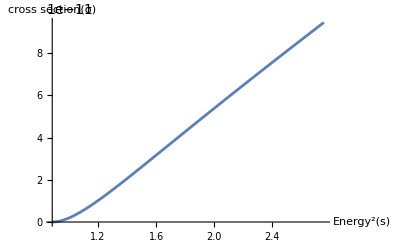

```mathematica
Plot[0.4*sigma[s],{s,lower[[1]],upper[[1]]}, Axes->True,AxesLabel->{(Energy^2)[s],cross section[σ]}]
```